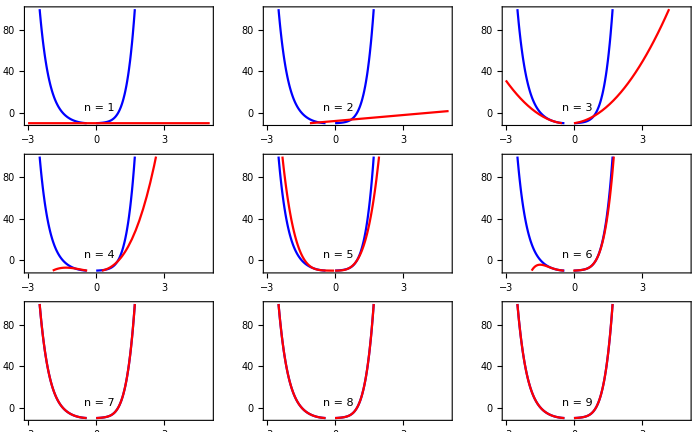

```mathematica
ChebyshevApprox[n_Integer?Positive,f_Function,x_]:=Module[{c,xk},xk=Pi (Range[n]-1/2)/n;
c[j_]=2*Total[Cos[j*xk]*(f/@Cos[xk])]/n;
Total[Table[c[k]*ChebyshevT[k,x],{k,0,n-1}]]-c[0]/2];

f=#^6+3*#^5+4*#^4+1/3*#^3+2*#^2+#-10&;

GraphicsGrid[Partition[Table[Plot[{f[x],ChebyshevApprox[n,f,x]},{x,-3,5},Frame->True,Axes->False,PlotStyle->{Blue,Red},PlotRange->{-10,100},Epilog->Text["n = "<>ToString[n],{0.15,5}]],{n,9}],3],ImageSize->700]
```